```mathematica
Clear["Global`*"];
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Import Files

```mathematica
readMatlabComplex[file_]:=ToExpression[StringSplit[StringReplace[ReadList[file,"String"],{"e"->"*10^","i"->"*I"}],","]]
```

```mathematica
allFiles=FileNames["*.csv"];
allData=readMatlabComplex[#]&/@allFiles;
```

ToExpression::sntx: Invalid syntax in or before "sampl*Ing rat*10^: 78.125 MHz".
                                                                   ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator crossov*10^r 174.6 kHz".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator saturat*Ion +43.0 dB".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

```mathematica
numoffiles=Dimensions[allFiles][[1]];
index=Table[i,{i,1,numoffiles}];
fileswithindex=Thread[{index,allFiles}];
dataset=Table[allData[[i]][[19;;]],{i,1,numoffiles}];
numset=Table[Dimensions[dataset[[i]]][[1]],{i,1,numoffiles}];
fileswithindex
```

{{1,100100P_20230417_201152_HighResData.csv},{2,100100X_20230417_201126_HighResData.csv},{3,LPam0pm_10_20230412_214245_HighResData.csv},{4,LPam_10pm0_20230412_213845_HighResData.csv},{5,Lpamoffpmoff_20230412_212225_HighResData.csv},{6,LXam0pm_10_20230412_214340_HighResData.csv},{7,LXam_10pm0_20230412_213812_HighResData.csv},{8,LXamoffpmoff_20230412_212345_HighResData.csv},{9,offoffP2_20230417_201024_HighResData.csv},{10,offoffX2_20230417_201057_HighResData.csv}}

## Density matrix in Fock basis

```mathematica
bin=160; (*Dimension of Discretized quadrature value Better be even?*)
n=8;  (*Photon number cutoff*)
dim=n+1; (*Dimension of density matrix*)

(*Ensuring positive semidefiniteness, trace property*)
rr=LowerTriangularize[Array[Subscript[r,##]&,{dim,dim}]];
ii=LowerTriangularize[Array[Subscript[im,##]&,{dim,dim}]];
ii=ii-DiagonalMatrix[Diagonal[ii]];
ii=ⅈ*ii;
t=rr+ii;
(*Density Matrix*)
ρ= ConjugateTranspose[t] . t/Tr[ConjugateTranspose[t] . t] ;
```

## Fock State Wave Function

```mathematica
fn=16;(*Pre-caculation*) 
psi[m_,x_]=HermiteH[m,x]/(√(2^m m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
Tpsi=Table[psi[m,x],{m,0,fn}];
```

## Shot Noise Unit Estimation

```mathematica
size1=Dimensions[allData[[9]][[19;;]]];
size1=size1[[1]];
vacp=Table[allData[[9]][[19;;]][[i]][[2]],{i,1,size1}];
snu1=StandardDeviation[vacp]
mp=Mean[vacp]

size2=Dimensions[allData[[10]][[19;;]]];
size2=size2[[1]];
vacx=Table[allData[[10]][[19;;]][[i]][[2]],{i,1,size2}];
snu2=StandardDeviation[vacx]
mx=Mean[vacx]
(*Shot noise unit is manually fit to match vacuum data with our theoretical expectation*)
snu=(snu1+snu2)/1.5;
```

4.86853×10^-6

-0.0000116228

4.88555×10^-6

-0.0000116536

## Discretizing Phase Space of the Signal

```mathematica
slice=snu*n/(bin/2);
xevent=ConstantArray[0,bin+1];
pevent=ConstantArray[0,bin+1];

(*X-Quadrature of the Data*)
xsize=Dimensions[allData[[6]][[19;;]]];
xsize=xsize[[1]];
xquad=Table[allData[[6]][[19;;]][[i]][[2]],{i,1,xsize}];

(*P-Quadrature of the Data*)
psize=Dimensions[allData[[3]][[19;;]]];
psize=psize[[1]];
pquad=Table[allData[[3]][[19;;]][[i]][[2]],{i,1,psize}];
```

## Counting Events

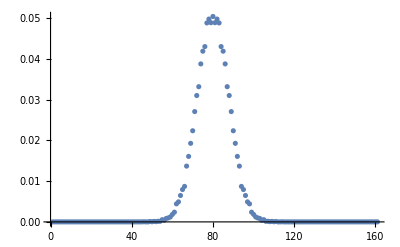

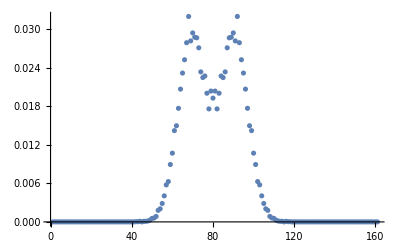

```mathematica
(*Counting Occurence*)
For[i=1,i<xsize+1,i++,
xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]=xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;

xevent[[-Round[(xquad[[i]]-mx)/slice]+bin/2]]=xevent[[-Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;]

For[i=1,i<psize+1,i++,
pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]=pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;

pevent[[-Round[(pquad[[i]]-mp)/slice]+bin/2]]=pevent[[-Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;]

(*Normalization*)
xevent=xevent/xsize/2;
pevent=pevent/psize/2;

(*Gmn is imported, discretized and normalized occurence of event*)
G={xevent,pevent}//N;
ListPlot[xevent, PlotRange->Full]
ListPlot[pevent,PlotRange->Full]
```

## Normalization Parameter for Projector

10.

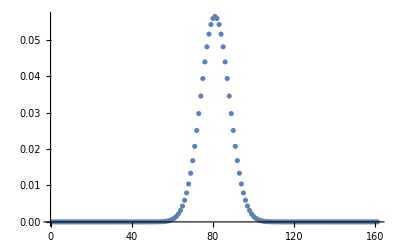

10.

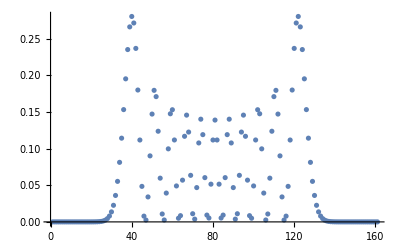

0.0136236

0.0145093

```mathematica
hermite0=Table[(psi[0,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm=Sum[hermite0[[i]],{i,1,bin+1}];
norm//N
hermite0=hermite0/norm;
ListPlot[hermite0,PlotRange->Full]
hermite1=Table[(psi[10,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm1=Sum[hermite1[[i]],{i,1,bin+1}];
norm1//N
ListPlot[hermite1,PlotRange->Full]
(*Just to see the similarity real quick*)
StandardDeviation[xevent]//N
StandardDeviation[hermite0]//N
```

## Projector Represented in quadrature basis

```mathematica
(*Matrix Element in Fock basis*)
Π=Table[(Tpsi[[a+1]]Tpsi[[b+1]]/norm)ⅇ^(ⅈ(b-a)θ),{a,0,n},{b,0,n}] ;
```

## Discretize X and θ

```mathematica
theta={0,Pi/2};
quad=Subdivide[-n,n,bin];
```

## Deviation Function

```mathematica
(*note that we do not use mean photon number because phase averaged measurement is not available*)
Q=Re[
Sum[(      G[[j,i]]-(  Tr[Π.ρ]/.{x->quad[[i]],θ->theta[[j]]}  )   )^2,{i,1,bin+1},{j,1,2}]
];
```

## Optimization Kernel

```mathematica
flat1=DeleteCases[Flatten[rr],_Integer];
flat2=DeleteCases[Flatten[-ⅈ*ii],_Integer];
kernel=Join[flat1,flat2];
```

## Maximum Entropy reconstruction

```mathematica
solution=FindMinimum[Q,kernel];

Chop[ρ /. solution[[2]] ];

Chop[MatrixForm[ρ /. solution[[2]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(0.548378 | -0.0201033-0.00753843 ⅈ | -0.18796+0.0295556 ⅈ | 0.0300934+0.024476 ⅈ | 0.00834948-0.0134947 ⅈ | -0.00760573+0.00632596 ⅈ | -0.00408426+0.0094583 ⅈ | 0.000332404+0.00616883 ⅈ | -0.0000241648+0.0000131597 ⅈ
-0.0201033+0.00753843 ⅈ | 0.330962 | -0.0258639-0.0143836 ⅈ | -0.0683118-0.00229579 ⅈ | 0.0107536+0.0100788 ⅈ | -0.00422833-0.00297003 ⅈ | -0.00331716+0.004425 ⅈ | -0.00410171-0.0000373769 ⅈ | -8.67903×10^-6-0.0000158962 ⅈ
-0.18796-0.0295556 ⅈ | -0.0258639+0.0143836 ⅈ | 0.0932416 | -0.00465401-0.0183584 ⅈ | -0.00754374+0.00502958 ⅈ | 0.00498644-0.00201439 ⅈ | 0.003028-0.00467637 ⅈ | 0.00125785-0.00315238 ⅈ | 0.0000151783-1.1581×10^-6 ⅈ
0.0300934-0.024476 ⅈ | -0.0683118+0.00229579 ⅈ | -0.00465401+0.0183584 ⅈ | 0.0233535 | -0.0021724-0.00427007 ⅈ | 0.000430856+0.00142439 ⅈ | 0.000832651-0.0005469 ⅈ | 0.00117525+0.000502072 ⅈ | 5.40775×10^-7+5.50686×10^-6 ⅈ
0.00834948+0.0134947 ⅈ | 0.0107536-0.0100788 ⅈ | -0.00754374-0.00502958 ⅈ | -0.0021724+0.00427007 ⅈ | 0.00179879 | -0.000688518-0.000235503 ⅈ | -0.000561084+0.000258396 ⅈ | -0.000620932+0.000281048 ⅈ | -2.35986×10^-6-1.88016×10^-6 ⅈ
-0.00760573-0.00632596 ⅈ | -0.00422833+0.00297003 ⅈ | 0.00498644+0.00201439 ⅈ | 0.000430856-0.00142439 ⅈ | -0.000688518+0.000235503 ⅈ | 0.000741032 | 0.000322287-0.000408183 ⅈ | 0.000174877-0.000301147 ⅈ | 1.53311×10^-6+1.06369×10^-7 ⅈ
-0.00408426-0.0094583 ⅈ | -0.00331716-0.004425 ⅈ | 0.003028+0.00467637 ⅈ | 0.000832651+0.0005469 ⅈ | -0.000561084-0.000258396 ⅈ | 0.000322287+0.000408183 ⅈ | 0.00106686 | 0.000505325+0.0000685794 ⅈ | 7.49993×10^-7+2.21537×10^-6 ⅈ
0.000332404-0.00616883 ⅈ | -0.00410171+0.0000373769 ⅈ | 0.00125785+0.00315238 ⅈ | 0.00117525-0.000502072 ⅈ | -0.000620932-0.000281048 ⅈ | 0.000174877+0.000301147 ⅈ | 0.000505325-0.0000685794 ⅈ | 0.000458472 | 9.4723×10^-7+1.83044×10^-6 ⅈ
-0.0000241648-0.0000131597 ⅈ | -8.67903×10^-6+0.0000158962 ⅈ | 0.0000151783+1.1581×10^-6 ⅈ | 5.40775×10^-7-5.50686×10^-6 ⅈ | -2.35986×10^-6+1.88016×10^-6 ⅈ | 1.53311×10^-6-1.06369×10^-7 ⅈ | 7.49993×10^-7-2.21537×10^-6 ⅈ | 9.4723×10^-7-1.83044×10^-6 ⅈ | 9.27689×10^-9)

## Plotting Real part of Density Matrix

```mathematica
DiscretePlot3D[Abs@Re[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Plotting Imaginary part

```mathematica
DiscretePlot3D[Abs@Im[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Wigner Reconstruction

```mathematica
g=2;
M=4;
xrange={-5,5};
yrange={-5,5};
linespace=100;
rho=ρ /. solution[[2]];
%//MatrixForm;
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx,yy}=meshgrid[Array[#&,linespace,xrange],Array[#&,linespace,yrange]];
aa=0.5*g*(xx+ⅈ yy);
%//MatrixForm;
wlist=Table[Table[Table[0,{i,1,M}],{j,1,M}],{k,1,M}];
wlist[[1]]=Exp[-2 Abs[aa]^2]/π;
W=Re[rho[[1,1]]]*Re[wlist[[1]]];

For[nn=1, nn<M,nn++,
wlist[[nn+1]]=(2.0*aa*wlist[[nn]])/√nn;
W+=2*Re[rho[[1,nn+1]]*wlist[[nn+1]]];
]


For[mm=1, mm<M,mm++,

temp=wlist[[mm+1]];
wlist[[mm+1]]=(2*Conjugate[aa]*temp-√mm*wlist[[mm]])/√mm;
W+=Re[rho[[mm+1,mm+1]]*wlist[[mm+1]]];
For[nn=mm+1, nn<M,nn++,
temp2=(2*aa*wlist[[nn]]-√mm*temp)/√nn;
temp=wlist[[nn+1]];
wlist[[nn+1]]=temp2;
W+=2*Re[rho[[mm+1,nn+1]]*wlist[[nn+1]]];
]
]
(*Plotting Wigner function. Grid not properly drawn yet*)
ListPlot3D[0.5*W*g^2,PlotRange->All, Boxed->False,DataRange->{{-5,5},{-5,5}}]
(*Displacement parameter*)
list=0.5*W*g^2;
pos=Position[list,_?(#==Max[list]&)]
disp=Sqrt[((50-pos[[1,1]])/10)^2+((50-pos[[1,2]])/10)^2]//N
```

-Graphics3D-

{{58,49}}

0.806226